```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 342 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[V]
V = -k/2 x[t]^2 + 1/2 λ0 x[t]^2 y[t]^2 + 1/4 λ1 x[t]^4
```

-1/2 k x[t]^2+1/4 λ1 x[t]^4+1/2 λ0 x[t]^2 y[t]^2

```mathematica
Clear[q]
q = { x[t] , y[t] }
```

{x[t],y[t]}

```mathematica
D[q, t]
```

{x'[t],y'[t]}

```mathematica
D[q, t] . D[q, t]
```

x'[t]^2+y'[t]^2

```mathematica
Clear[T]
T = 
1/2 m ( D[q, t] . D[q, t]  )
```

1/2 m (x'[t]^2+y'[t]^2)

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

1/2 k (x(t))^2+1/2 m (((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2)-1/4 λ1 (x(t))^4-1/2 λ0 (x(t))^2 (y(t))^2

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-λ1 x[t]^3+x[t] (k-λ0 y[t]^2)-m x''[t]==0
-λ0 x[t]^2 y[t]-m y''[t]==0

```mathematica
Clear[parameters]
parameters = {
k-> 1 , 
m-> 1 , 
λ0-> 1 , 
λ1-> 1
} ;
parameters // TableForm
```

k→1
m→1
λ0→1
λ1→1

```mathematica
eqs /. parameters  // TableForm
```

-x[t]^3+x[t] (1-y[t]^2)-x''[t]==0
-x[t]^2 y[t]-y''[t]==0

```mathematica
Clear[ics]
ics = {
x[0] == 0.1 ,
x'[0] == 0.1 ,
y[0] == 0.1 ,
y'[0] == 0.1
} ;
ics // TableForm
```

x[0]==0.1
x'[0]==0.1
y[0]==0.1
y'[0]==0.1

```mathematica
Clear[solution]
solution[t_] =
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0 , 300 } ]]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

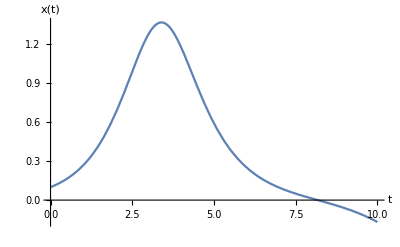

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[1]] }   ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,25 , 0.5  } ]
```

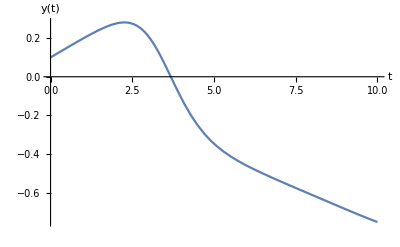

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[2]] }   ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,15 , 0.5  } ]
```

```mathematica
Clear[xyReplace]
xyReplace = { 
x[t]-> x , 
y[t] -> y } ;
xyReplace
```

{x[t]→x,y[t]→y}

```mathematica
Clear[parameters]
parameters = { 
k -> 1 , 
λ0-> 1 , 
λ1-> 1 } ;
parameters // TableForm
```

k→1
λ0→1
λ1→1

```mathematica
V /. parameters  /. xyReplace
```

-x^2/2+x^4/4+(x^2 y^2)/2

```mathematica
?Plot3D
```

```mathematica
Plot3D[ V /. parameters , { x[t] , -1.5 , 1.5 } , { y[t] , -1.5 , 1.5 }, AxesLabel-> { x[t] , y[t] ,"V" }  ] 
Plot3D[ V /. parameters /. xyReplace , { x,-1.5,1.5 } , { y,-1.5,1.5 } , AxesLabel-> { x , y , "V" }]
```

-Graphics3D-

-Graphics3D-

```mathematica
?FindMinimum
```

```mathematica
V /. parameters /. xyReplace
```

-x^2/2+x^4/4+(x^2 y^2)/2

```mathematica
FindMinimum[ V /. parameters  /. xyReplace  , { { x , 0.9 } , { y , 0.1 } }] (* Look at exponent on y value ~ 0 *)
```

{-0.25,{x→1.,y→2.27573×10^-11}}

```mathematica
FindMinimum[ V /. parameters , { { x[t] , 0.9 } , { y[t] , 0.1 } }] 
(* Look at exponent on y value ~ 0 *)
```

{-0.25,{x[t]→1.,y[t]→2.27573×10^-11}}

```mathematica
D[V, x[t]] == 0
```

-k x[t]+λ1 x[t]^3+λ0 x[t] y[t]^2==0

```mathematica
D[V, y[t]]== 0
```

λ0 x[t]^2 y[t]==0

```mathematica
D[V, { x[t] , 2 }] == 0
```

-k+3 λ1 x[t]^2+λ0 y[t]^2==0

```mathematica
D[V, { y[t] , 2 }] == 0
```

λ0 x[t]^2==0

```mathematica
Solve[Union[ D[V, x[t]] == 0  , D[V, y[t]]== 0  ] , q ] 
Solve[Union[ D[V, x[t]] == 0  , D[V, y[t]]== 0  ] , q ] [[2]]
Solve[Union[ D[V, x[t]] == 0  , D[V, y[t]]== 0  ] , q ] [[3]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[t]→0},{x[t]→-(√k)/(√λ1),y[t]→0},{x[t]→(√k)/(√λ1),y[t]→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{x[t]→-(√k)/(√λ1),y[t]→0}

Solve::svars: Equations may not give solutions for all "solve" variables.

{x[t]→(√k)/(√λ1),y[t]→0}

```mathematica
({{D[D[V, x[t]], x[t]], D[D[V, y[t]], x[t]]}, {D[D[V, x[t]], y[t]], D[D[V, y[t]], y[t]]}}) // MatrixForm
```

(-k+3 λ1 x[t]^2+λ0 y[t]^2 | 2 λ0 x[t] y[t]
2 λ0 x[t] y[t] | λ0 x[t]^2)

```mathematica
Det[ ({{D[D[V, x[t]], x[t]], D[D[V, y[t]], x[t]]}, {D[D[V, x[t]], y[t]], D[D[V, y[t]], y[t]]}})] /. parameters
```

-x[t]^2+3 x[t]^4-3 x[t]^2 y[t]^2

```mathematica
Det[ ({{D[D[V, x[t]], x[t]], D[D[V, y[t]], x[t]]}, {D[D[V, x[t]], y[t]], D[D[V, y[t]], y[t]]}})] /. parameters  /. x[t]-> 1 /. y[t]-> 0
```

2

```mathematica
Det[ ({{D[D[V, x[t]], x[t]], D[D[V, y[t]], x[t]]}, {D[D[V, x[t]], y[t]], D[D[V, y[t]], y[t]]}})] /. parameters  /. x[t]-> - 1 /. y[t]-> 0
```

2

```mathematica
(* Need to do multivariable Taylor Series before substituion *)
```

```mathematica
Clear[𝓍𝓎Replace]
𝓍𝓎Replace = 
Solve[ { 𝓍[t] == x[t] - √(k/λ1), 𝓎[t] == y[t] }  , { x[t] , y[t] }]  // Flatten
(* See typo in book λ needs to be λ1 *)
```

{x[t]→√(k/λ1)+𝓍[t],y[t]→𝓎[t]}

```mathematica
D[𝓍𝓎Replace, t]
```

{x'[t]→𝓍'[t],y'[t]→𝓎'[t]}

```mathematica
ℒ  /. 𝓍𝓎Replace
```

1/2 k (√(k/λ1)+𝓍[t])^2-1/4 λ1 (√(k/λ1)+𝓍[t])^4-1/2 λ0 (√(k/λ1)+𝓍[t])^2 𝓎[t]^2+1/2 m (x'[t]^2+y'[t]^2)

```mathematica
ℒ  /. 𝓍𝓎Replace /. D[𝓍𝓎Replace, t]
```

1/2 k (√(k/λ1)+𝓍[t])^2-1/4 λ1 (√(k/λ1)+𝓍[t])^4-1/2 λ0 (√(k/λ1)+𝓍[t])^2 𝓎[t]^2+1/2 m (𝓍'[t]^2+𝓎'[t]^2)

```mathematica
ℒ  /. 𝓍𝓎Replace /. D[𝓍𝓎Replace, t]  // Expand
```

k^2/(4 λ1)-k 𝓍[t]^2-√(k/λ1) λ1 𝓍[t]^3-1/4 λ1 𝓍[t]^4-(k λ0 𝓎[t]^2)/(2 λ1)-λ0 √(k/λ1) 𝓍[t] 𝓎[t]^2-1/2 λ0 𝓍[t]^2 𝓎[t]^2+1/2 m 𝓍'[t]^2+1/2 m 𝓎'[t]^2

```mathematica
ℒ  /. 𝓍𝓎Replace /. D[𝓍𝓎Replace, t]  // Expand  // Simplify
```

(k^2-4 √(k/λ1) λ1^2 𝓍[t]^3-λ1^2 𝓍[t]^4-2 k λ0 𝓎[t]^2-4 λ0 √(k/λ1) λ1 𝓍[t] 𝓎[t]^2-2 λ1 𝓍[t]^2 (2 k+λ0 𝓎[t]^2)+2 m λ1 𝓍'[t]^2+2 m λ1 𝓎'[t]^2)/(4 λ1)